## Data

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import ["task1.csv"];
claassMinus1=data[[Flatten@Position[data[[All,3]],-1]]];
claassMinus2=data[[Flatten@Position[data[[All,3]],1]]];
n=Length@data;
```

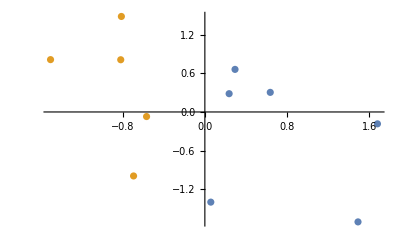

```mathematica
ListPlot[{claassMinus1[[All,;;2]],claassMinus2[[All,;;2]]}]
```

## Linear Kernel

```mathematica
lmbd=Array[λ,n];
x={x1,x2};
X=Transpose[{data⟦All,1⟧,data⟦All,2⟧}];
Y=data⟦All,3⟧;
L=Total[lmbd]-0.5*Sum[(lmbd⟦i⟧*lmbd⟦j⟧*Y⟦i⟧*Y⟦j⟧)*(X⟦i⟧.X⟦j⟧),{i,1,n},{j,1,n}];
condition=Total[lmbd*Y];
```

```mathematica
res=NMaximize[{L,lmbd≥0,condition==0},lmbd]
```

{3.44173,{λ[1]→0.890406,λ[2]→2.5517,λ[3]→0.,λ[4]→0.,λ[5]→3.44211,λ[6]→0.,λ[7]→0.,λ[8]→0.,λ[9]→0.,λ[10]→0.,λ[11]→0.}}

## Show Result

```mathematica
output=lmbd/.res[[2]];
θ=Total[output*Y*X];
θ0=Sum[Y⟦i⟧-θ.X⟦i⟧,{i,1,n}]/n;
plos=θ.x+θ0
resu=First[Flatten@Solve[plos==0,x2]][[2]]
```

-0.0909091-2.60925 x1+0.277109 x2

3.60869 (0.0909091+2.60925 x1)

```mathematica
fun[resu_,x_]:=resu/.{x1->x}
```

```mathematica
points=Table[{x,fun[resu,x]},{x,-2,2,0.1}];
```

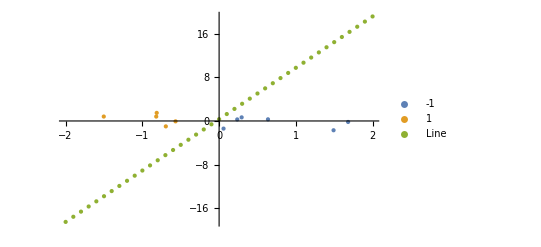

```mathematica
ListPlot[{claassMinus1[[All,;;2]],claassMinus2[[All,;;2]],points},PlotLegends->{-1,1,"Line"},PlotStyle->PointSize[Medium]]
```